# Testing Nadolsky, Stump, Yuan (hep-ph/9906280) Asymptotic, Fixed Order and Y - term with toy models for PDFs and FFs. - Calculate only A_1 term - Examine only quark-in-quark terms - Calculate for one flavor - Use 3-flavor alpha strong - Drop factors of A_1, σ_0, 1/(4π),1/S_eA, etc...

```mathematica
Clear["Global *"];
```

## Basic Parameters

```mathematica
Lambda = 0.339;   
nf = 3;
CF = 4/3;
beta0 := 11-2*nf/3;
beta1 := 102-38*nf/3;
muval = 10;(** Typical hard scale. **)
```

## Alpha Strong

```mathematica
stdloops = 2;
alpiN[mu_,loops_] := 2/( beta0 * Log[mu/Lambda]) +
                                        If[ loops > 1, (-beta1*Log[2*Log[mu/Lambda]] / (beta0^3 * Log[mu/Lambda]^2 )), 0];
alpi[mu_] := alpiN[mu,stdloops]
```

## Toy Model of quark in quark PDF:

```mathematica
pdf[x_,mu_]:=10.5912(x^(.8 - .07 Log[mu/.2])) (1 - x)^1.1
```

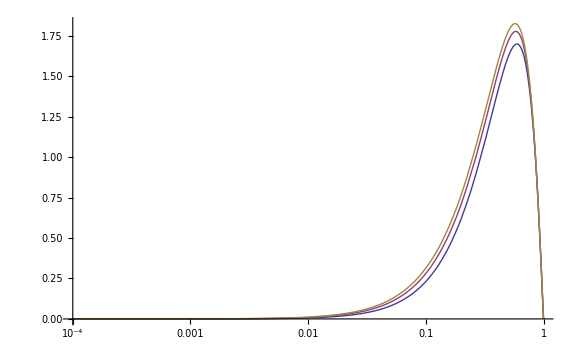

```mathematica
LogLinearPlot[{x pdf[x,3],x pdf[x,10],x pdf[x,20]},{x,.0001,1}]
```

```mathematica
1/ Integrate[x pdf[x,2],{x,0,1}]
```

1.

```mathematica
(*DBC wire in the PDFs here. which flavor? do we look at all of them?*)
```

## Toy Model of quark in quark Fragmentation Function

```mathematica
frag[z_,mu_] :=5.5546(z^(.04- .01 Log[mu/.1])) (1 - z)^.9
```

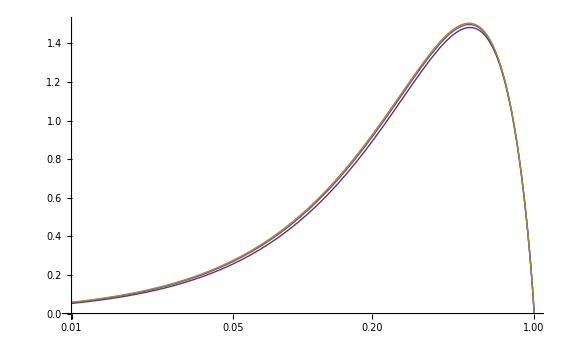

```mathematica
LogLinearPlot[{z frag[z,2],z frag[z,10],z frag[z,20]},{z,.01,1}]
```

```mathematica
1/ Integrate[z frag[z,2],{z,0,1}]
```

1.

## The fixed order term (FO): Ref.[1] Eq.(B1) and Eq.(B2).

```mathematica
xhat[x_,xia_]:= x / xia; (** Definition of x̂, Eq.(25) **)
zhat1[xh_,qt_,Q_]:= (1 - xh) / (((qt^2/Q^2) - 1)xh + 1) (** Value of ẑ fixed by δ function, Eq.(B7), in terms of arbitrary xh. **)
```

```mathematica
zhat[x_,xia_,qt_,Q_] := zhat1[xhat[x,xia],qt,Q]  (** Eq.(B7) at true value of x̂. **)
```

### Factor in Eq.(B2).

```mathematica
Coeff[Q_,qt_,xia_,x_,mu_]:= 2 CF alpi[mu]xhat[x,xia] zhat[x,xia,qt,Q]((1/(qt^2)) ((Q^4/(xhat[x,xia]^2 zhat[x,xia,qt,Q]^2)) + (Q^2 - qt^2)^2) + 6 Q^2)
```

### Overall factor from evaluating the δ function in Eq.(B1).

```mathematica
Jaco[z_,x_,xia_]:= z xhat[x,xia]/(1 - xhat[x,xia])
```

### Integrand in Eq just before Eq.(B1).

```mathematica
Integranda[Q_,qt_,z_,xia_,x_,mu_]:= Re[ Jaco[z,x,xia]Coeff[Q,qt,xia,x,mu](pdf[xia,mu]/xia)(frag[z/zhat[x,xia,qt,Q],mu] /(z/zhat[x,xia,qt,Q]))HeavisideTheta[zhat[x,xia,qt,Q]-z]]/Q^2
```

### Term with A and B switched:

```mathematica
Integrandb[Q_,qt_,z_,xia_,x_,mu_]:= Re[ Jaco[z,x,xia]Coeff[Q,qt,xia,x,mu](frag[xia,mu]/xia)(pdf[z/zhat[x,xia,qt,Q],mu] /(z/zhat[x,xia,qt,Q]))HeavisideTheta[zhat[x,xia,qt,Q]-z]]/Q^2
```

### Sum of quark-to-quark terms in integrand in Eq.(B1):

```mathematica
FixedOrder[Q_,qt_,z_,x_,mu_] := NIntegrate[Integranda[Q,qt,z,xia,x,mu],{xia,x,1}]+NIntegrate[Integrandb[Q,qt,z,xia,x,mu],{xia,x,1}]
```

## The Asymptotic term (ASY): Eq.(36) in Ref.[1].

### Define the Plus Distribution in Eq.(39,40):

```mathematica
SetAttributes[{PlusDist,pdfconvo,ffconvo},HoldAll];
```

```mathematica
PlusDist[minval_,f_[xmin_,x_,mu_]]:= NIntegrate[((1 + x^2) f[xmin,xmin /x,mu]/x - 2 f[xmin,xmin,mu])/(1-x),{x,minval,1}] + 2 f[xmin,xmin,mu]Log[1 - minval]
```

### The PDF and Fragmentation Function in a form for convolution with the + distribution:

```mathematica
pdfconvo[x_,xi_,mu_]:=pdf[x/xi,mu]
ffconvo[z_,xi_,mu_]:= frag[z/xi,mu]
```

### The qaurk-to-quark terms in Eq.(36):

```mathematica
(** First Term in Eq.(40). **)
AsyTerm1[z_,x_,mu_]:= frag[z,mu] PlusDist[x,pdfconvo[x,xi,mu]]
```

```mathematica
(** Third Term in Eq.(40). **)
AsyTerm3[z_,x_,mu_]:= pdf[x,mu] PlusDist[z,ffconvo[z,xi,mu]]
```

```mathematica
(** Fifth Term in Eq.(40). **)
AsyTerm5[z_,x_,mu_,qt_] := 2 pdf[x,mu] frag[z,mu] (CF( Log[mu^2/qt^2] - (3/2)))
```

### Some sample values:

```mathematica
AsyTerm1[.8,.1,muval]
AsyTerm3[.8,.1,muval]
AsyTerm5[.8,.1,muval,4.0]
```

21.5974

8.20825

3.25452

### Complete Asymptotic part (with alpha strong and 1/q_T^2)

```mathematica
Asymptot[ex_,z_,mu_,qt_]:=(alpi[mu]/(qt^2))(AsyTerm1[ex,z,mu] + AsyTerm3[ex,z,mu] + AsyTerm5[ex,z,mu,qt])
```

## Plot of Both Fixed Order and Asymptotic Parts:

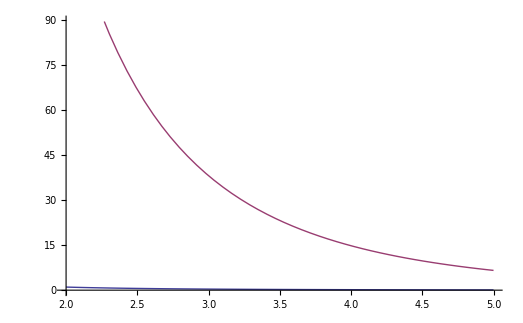

```mathematica
Plot[{Asymptot[.1,.8,muval,qt],FixedOrder[10,qt,.8,.1,muval]},{qt,2,5}]
```

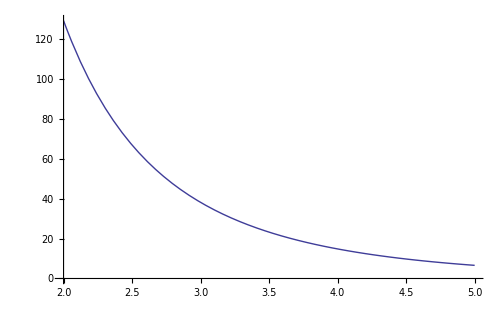

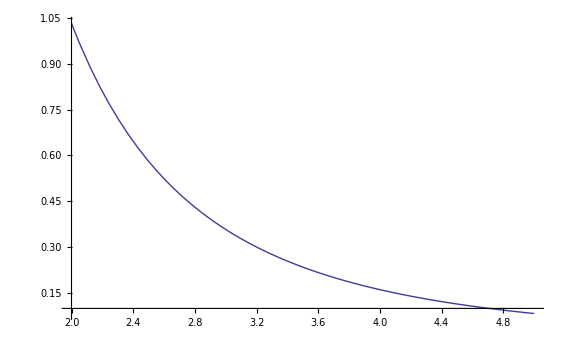

```mathematica
Plot[{FixedOrder[10,qt,.8,.1,muval]},{qt,2,5}]
Plot[{Asymptot[.1,.8,muval,qt]},{qt,2,5}]
```